## Load package

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["diffTVR`"]
```

```mathematica
?diffTVR`*
```

# Absolute value, white noise

## Data

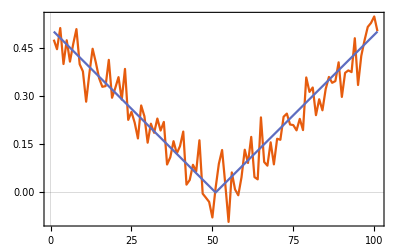

```mathematica
dx=0.01;
dataExact=Table[Abs[x-0.5],{x,0,1,dx}];
dataNoisy=Table[x+RandomVariate[NormalDistribution[0,0.05]],{x,dataExact}];
pltData=ListLinePlot[{dataNoisy,dataExact}]
```

```mathematica
diff[x_]:=(RotateLeft[x]-x)[[;;-2]]/(dx)
```

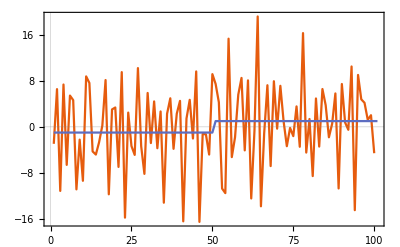

```mathematica
derivExact=Table[If[x<0.5,-1,1],{x,0,1,dx}];
derivNoisy=diff[dataNoisy];
pltDeriv=ListLinePlot[{derivNoisy,derivExact}]
```

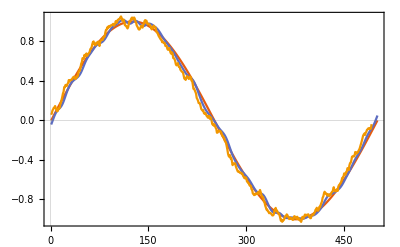

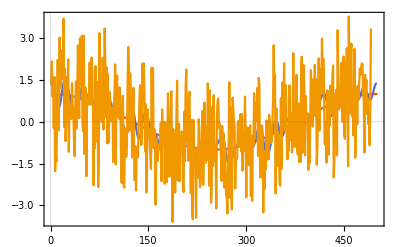

```mathematica
dataFiltered=LowpassFilter[dataNoisy,0.2];
dataAve=MovingAverage[dataNoisy,10];
ListLinePlot[{dataExact,dataFiltered,dataAve}]

derivFiltered=diff[dataFiltered];
derivAve=diff[dataAve];
ListLinePlot[{derivExact,derivFiltered,derivAve}]
```

## Diff TVR

```mathematica
derivGuess=ConstantArray[0,Length[dataNoisy]+1];
noOptSteps=100;
alpha=0.2;
derivFinal=getDiffTVR[dataNoisy,derivGuess,noOptSteps,dx,alpha];
```

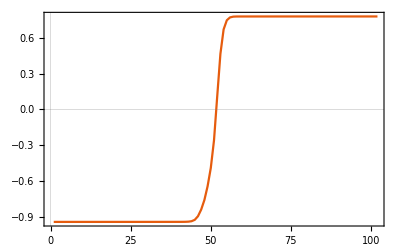

```mathematica
ListLinePlot[derivFinal]
```

# Absolute value, uniform noise

## Data

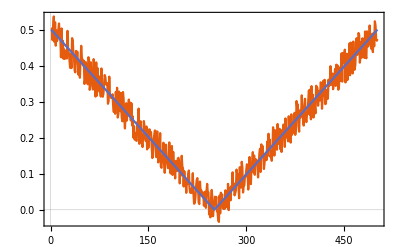

```mathematica
dx=0.002;
dataExact=Table[Abs[x-0.5],{x,0,1,dx}];
dataNoisy=Table[x+0.05*RandomReal[{-1,1}],{x,dataExact}];
pltData=ListLinePlot[{dataNoisy,dataExact}]
```

```mathematica
diff[x_]:=(RotateLeft[x]-x)[[;;-2]]/(dx)
```

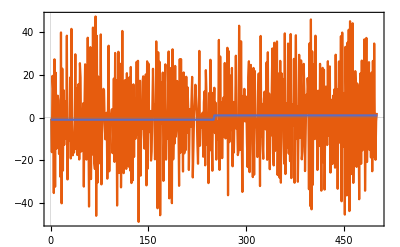

```mathematica
derivExact=Table[If[x<0.5,-1,1],{x,0,1,dx}];
derivNoisy=diff[dataNoisy];
pltDeriv=ListLinePlot[{derivNoisy,derivExact}]
```

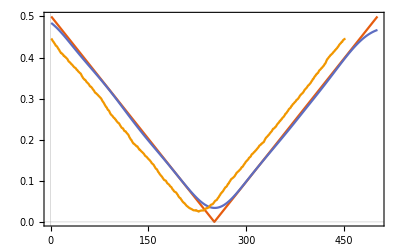

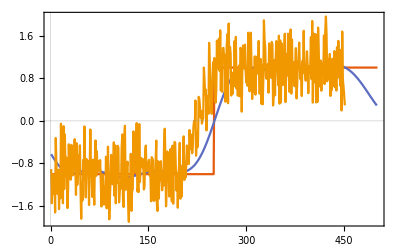

```mathematica
dataFiltered=LowpassFilter[dataNoisy,0.05];
dataAve=MovingAverage[dataNoisy,50];
ListLinePlot[{dataExact,dataFiltered,dataAve}]

derivFiltered=diff[dataFiltered];
derivAve=diff[dataAve];
ListLinePlot[{derivExact,derivFiltered,derivAve}]
```

## Diff TVR

```mathematica
derivGuess=ConstantArray[0,Length[dataNoisy]+1];
noOptSteps=100;
alpha=0.2;
derivFinal=getDiffTVR[dataNoisy,derivGuess,noOptSteps,dx,alpha];
```

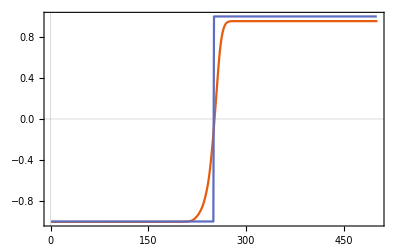

```mathematica
ListLinePlot[{derivFinal,derivExact}]
```

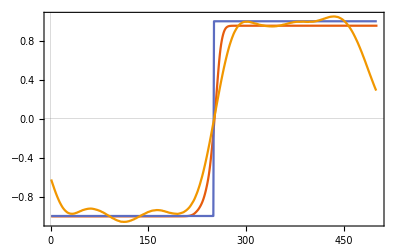

```mathematica
ListLinePlot[{derivFinal,derivExact,derivFiltered}]
```

# Damped sin function, uniform noise

```mathematica
diff[x_]:=(RotateLeft[x]-x)[[;;-2]]/(dx)
```

```mathematica
integrate[pt1_,deriv_]:=Flatten[{pt1,pt1+(Accumulate[deriv]-0.5*(deriv+deriv[[1]]))*dx}];
```

```mathematica
err[true_,signal_]:=Module[
{ml,max,min},
ml=Min[Length[signal],Length[true]];
max=Max[true[[;;ml]]];
min=Min[true[[;;ml]]];
Style[Text[Mean[Abs[signal[[;;ml]]-true[[;;ml]]]/(max-min)]],FontSize->24]
]
```

## Data

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
styleExactF=Darker[Green];
styleExact=Opacity[0.4,Darker[Green]];
styleNoisy=Directive[Opacity[0.7],colors[[1]]];
styleFiltered1=colors[[2]];
styleFiltered2=Darker[Magenta];
styleAve=Brown;
styleTVR=Black;
styleTVRFiltered=Gray;
styleFiltered1Filtered=Lighter[styleFiltered1];
styleFiltered2Filtered=Lighter[styleFiltered2];
styleNoisyFiltered=Blue;
```

```mathematica
rowLabels={
Null,
Style[Text["Signal"],FontSize->24],
Style[Text["Derivative"],FontSize->24],
Style[Text["Integrated"],FontSize->24],
Style[Text["Derivative \n error estimate"],FontSize->24],
Style[Text["Signal \n error estimate"],FontSize->24]
};
```

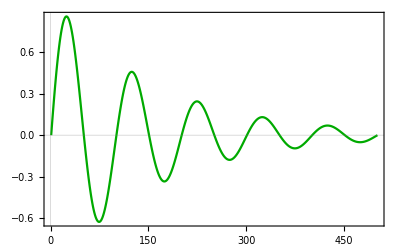
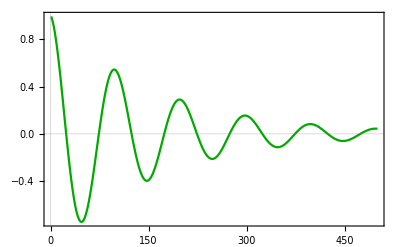
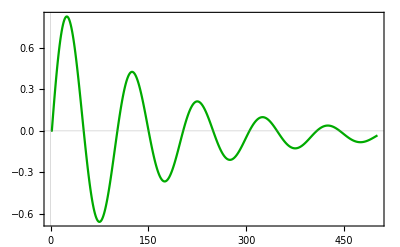
| Signal | Derivative | Integrated | Derivative 
 error estimate | Signal 
 error estimate
Exact signal 
 -> Differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- |  |

```mathematica
dx=10*Pi/500.0;
dataExact=Table[Sin[x]*Exp[-0.1*x],{x,0,10*Pi,dx}];
derivExact=diff[dataExact];(*Table[Cos[x]*Exp[-0.1*x]-0.1*Sin[x]*Exp[-0.1*x],{x,0,10*Pi,dx}];*)
rowExact={
Style[Text["Exact signal \n -> Differentiate \n -> Integrate"],FontSize->24],
ListLinePlot[dataExact,PlotStyle->styleExactF],
ListLinePlot[derivExact,PlotStyle->styleExactF],
ListLinePlot[integrate[dataExact[[1]],derivExact],PlotStyle->styleExactF]
};
Grid[{rowLabels,rowExact}]
```

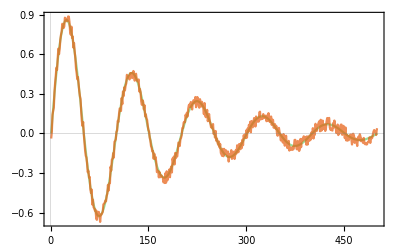
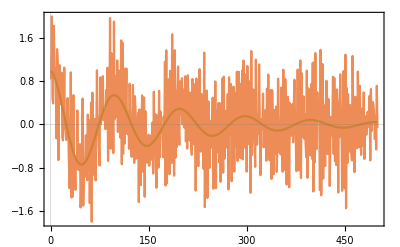
| Signal | Derivative | Integrated | Derivative 
 error estimate | Signal 
 error estimate
Noisy signal 
 -> Differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- |  |

```mathematica
dx=10*Pi/500.0;
dataNoisy=Table[x+0.05*RandomReal[{-1,1}],{x,dataExact}];
derivNoisy=diff[dataNoisy];
rowNoisy={
Style[Text["Noisy signal \n -> Differentiate \n -> Integrate"],FontSize->24],
ListLinePlot[{dataExact,dataNoisy},PlotStyle->{styleExact,styleNoisy}],
ListLinePlot[{derivExact,derivNoisy},PlotStyle->{styleExact,styleNoisy}],
ListLinePlot[{dataExact,dataNoisy},PlotStyle->{styleExact,styleNoisy}]
};
Grid[{rowLabels,rowNoisy}]
```

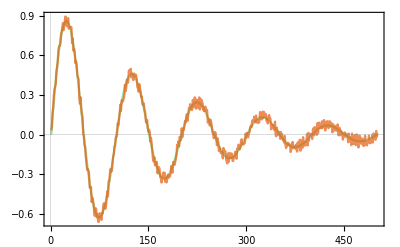
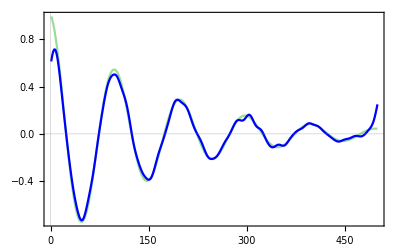
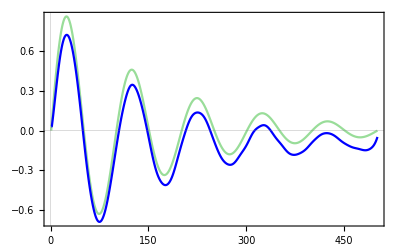
| Signal | Derivative | Integrated | Derivative 
 error estimate | Signal 
 error estimate
Noisy signal 
 -> Differentiate -> low-pass (0.2) 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.011622 | 0.062012

```mathematica
derivNoisyFiltered=LowpassFilter[derivNoisy,0.2];
rowNoisyFiltered={
Style[Text["Noisy signal \n -> Differentiate -> low-pass (0.2) \n -> Integrate"],FontSize->24],
ListLinePlot[{dataExact,dataNoisy},PlotStyle->{styleExact,styleNoisy}],
ListLinePlot[{derivExact,derivNoisyFiltered},PlotStyle->{styleExact,styleNoisyFiltered},PlotRange->All],
ListLinePlot[{dataExact,integrate[dataNoisy[[1]],derivNoisyFiltered]},PlotStyle->{styleExact,styleNoisyFiltered}],
err[derivExact,derivNoisyFiltered],
err[dataExact,integrate[dataNoisy[[1]],derivNoisyFiltered]]
};
Grid[{rowLabels,rowNoisyFiltered}]
```

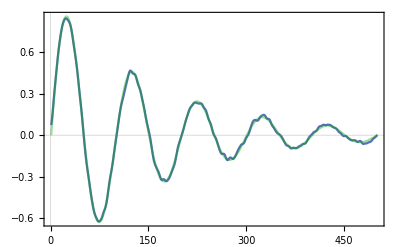
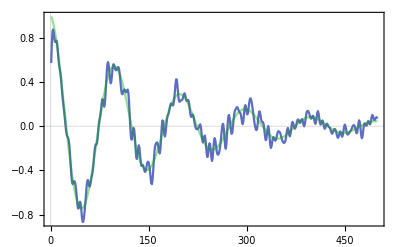
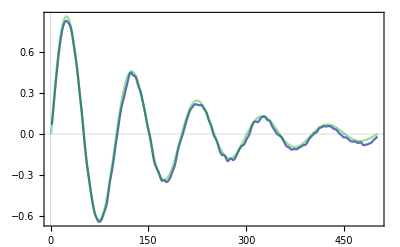
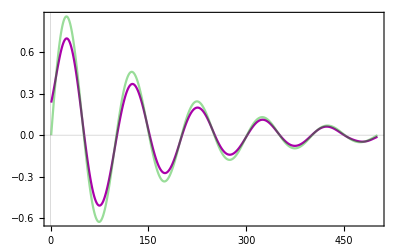
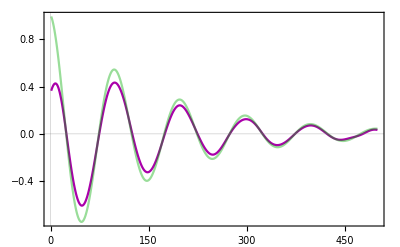
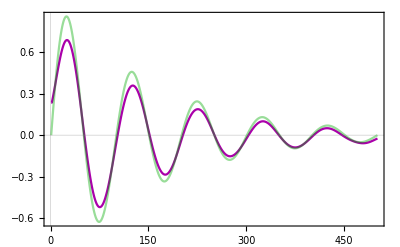
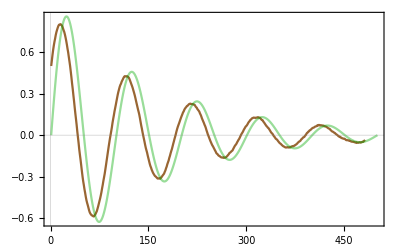
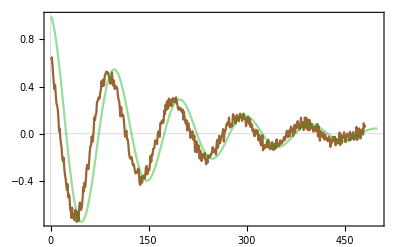
| Signal | Derivative | Integrated | Derivative 
 error estimate | Signal 
 error estimate
Noisy signal -> low-pass (0.5) 
 -> Differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.026813 | 0.0125719
Noisy signal -> low-pass (0.1) 
 -> Differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.0255266 | 0.0262913
Noisy signal -> moving average (20) 
 -> Differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.0688079 | 0.0711493

```mathematica
dataFiltered1=LowpassFilter[dataNoisy,0.5];
dataFiltered2=LowpassFilter[dataNoisy,0.1];
dataAve=MovingAverage[dataNoisy,20];

derivFiltered1=diff[dataFiltered1];
derivFiltered2=diff[dataFiltered2];
derivAve=diff[dataAve];

rowFiltered1={
Style[Text["Noisy signal -> low-pass (0.5) \n -> Differentiate \n -> Integrate"],FontSize->24],
ListLinePlot[{dataFiltered1,dataExact},PlotStyle->{styleFiltered1,styleExact}],
ListLinePlot[{derivFiltered1,derivExact},PlotStyle->{styleFiltered1,styleExact}],
ListLinePlot[{integrate[dataFiltered1[[1]],derivFiltered1],dataExact},PlotStyle->{styleFiltered1,styleExact}],
err[derivExact,derivFiltered1],
err[dataExact,integrate[dataFiltered1[[1]],derivFiltered1]]
};
rowFiltered2={
Style[Text["Noisy signal -> low-pass (0.1) \n -> Differentiate \n -> Integrate"],FontSize->24],
ListLinePlot[{dataFiltered2,dataExact},PlotStyle->{styleFiltered2,styleExact}],
ListLinePlot[{derivFiltered2,derivExact},PlotStyle->{styleFiltered2,styleExact}],
ListLinePlot[{integrate[dataFiltered2[[1]],derivFiltered2],dataExact},PlotStyle->{styleFiltered2,styleExact}],
err[derivExact,derivFiltered2],
err[dataExact,integrate[dataFiltered2[[1]],derivFiltered2]]
};
rowAve={
Style[Text["Noisy signal -> moving average (20) \n -> Differentiate \n -> Integrate"],FontSize->24],
ListLinePlot[{dataAve,dataExact},PlotStyle->{styleAve,styleExact}],
ListLinePlot[{derivAve,derivExact},PlotStyle->{styleAve,styleExact}],
ListLinePlot[{integrate[dataAve[[1]],derivAve],dataExact},PlotStyle->{styleAve,styleExact}],
err[derivExact,derivAve],
err[dataExact,integrate[dataAve[[1]],derivAve]]
};

Grid[{rowLabels,rowFiltered1,rowFiltered2,rowAve}]
```

## Diff TVR

```mathematica
derivGuess=ConstantArray[0,Length[dataNoisy]+1];
noOptSteps=100;
alpha=0.01;
derivFinal=getDiffTVR[dataNoisy,derivGuess,noOptSteps,dx,alpha];
```

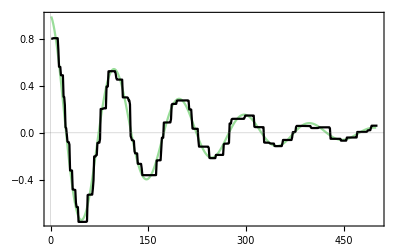
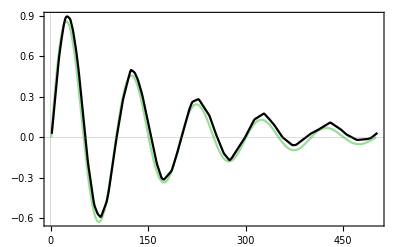
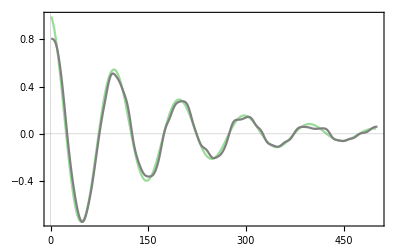
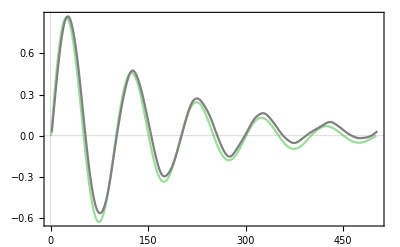
| Signal | Derivative | Integrated | Derivative 
 error estimate | Signal 
 error estimate
Noisy signal 
 -> TVR differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.0206918 | 0.0279454
Noisy signal 
 -> TVR differentiate -> low-pass (0.2) 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.0149498 | 0.0281908

```mathematica
derivFinalFiltered=LowpassFilter[derivFinal,0.25];

rrowTVR={
Style[Text["Noisy signal \n -> TVR differentiate \n -> Integrate"],FontSize->24],
ListLinePlot[{dataExact,dataNoisy},PlotStyle->{styleExact,styleNoisy}],
ListLinePlot[{derivExact,derivFinal},PlotStyle->{styleExact,styleTVR},PlotRange->All],
ListLinePlot[{dataExact,integrate[dataNoisy[[1]],derivFinal]},PlotStyle->{styleExact,styleTVR},PlotRange->All],
err[derivExact,derivFinal],
err[dataExact,integrate[dataNoisy[[1]],derivFinal]]
};
rrowTVRFiltered={
Style[Text["Noisy signal \n -> TVR differentiate -> low-pass (0.2) \n -> Integrate"],FontSize->24],
ListLinePlot[{dataExact,dataNoisy},PlotStyle->{styleExact,styleNoisy}],
ListLinePlot[{derivExact,derivFinalFiltered},PlotStyle->{styleExact,styleTVRFiltered},PlotRange->All],
ListLinePlot[{dataExact,integrate[dataNoisy[[1]],derivFinalFiltered]},PlotStyle->{styleExact,styleTVRFiltered},PlotRange->All],
err[derivExact,derivFinalFiltered],
err[dataExact,integrate[dataNoisy[[1]],derivFinalFiltered]]
};

Grid[{
rowLabels,
rrowTVR,
rrowTVRFiltered
}]
```

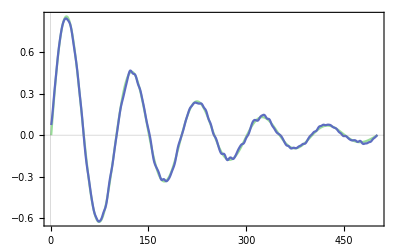
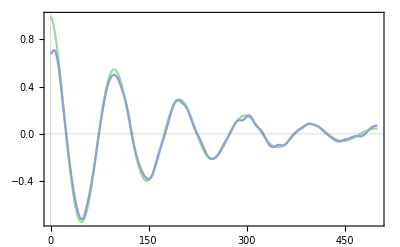
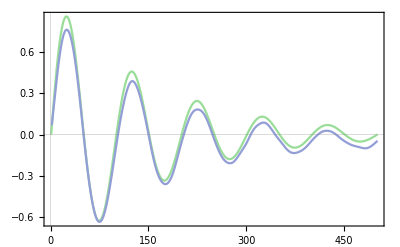
| Signal | Derivative | Integrated | Derivative 
 error estimate | Signal 
 error estimate
Noisy signal -> low-pass (0.5) 
 -> Differentiate -> low-pass filter (0.2) 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.0107378 | 0.0303863

```mathematica
derivFiltered1Filtered=LowpassFilter[derivFiltered1,0.2];

rrowFiltered1Filtered={
Style[Text["Noisy signal -> low-pass (0.5) \n -> Differentiate -> low-pass filter (0.2) \n -> Integrate"],FontSize->24],
ListLinePlot[{dataExact,dataFiltered1},PlotStyle->{styleExact,styleFiltered1},PlotRange->All],
ListLinePlot[{derivExact,derivFiltered1Filtered},PlotStyle->{styleExact,styleFiltered1Filtered},PlotRange->All],
ListLinePlot[{dataExact,integrate[dataFiltered1[[1]],derivFiltered1Filtered]},PlotStyle->{styleExact,styleFiltered1Filtered},PlotRange->All],
err[derivExact,derivFiltered1Filtered],
err[dataExact,integrate[dataFiltered1[[1]],derivFiltered1Filtered]]
};

Grid[{
rowLabels,
rrowFiltered1Filtered
}]
```

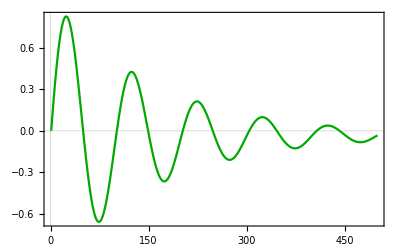
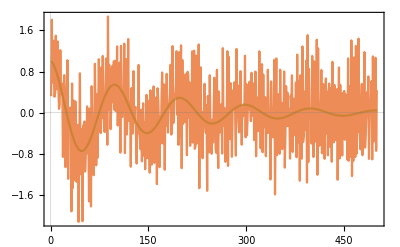
| Signal | Derivative | Integrated | Derivative 
 error estimate | Signal 
 error estimate
Exact signal 
 -> Differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- |  | 
Noisy signal 
 -> Differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- |  | 
Noisy signal 
 -> Differentiate -> low-pass (0.2) 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.011622 | 0.062012
Noisy signal -> low-pass (0.5) 
 -> Differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.026813 | 0.0125719
Noisy signal -> low-pass (0.1) 
 -> Differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.0255266 | 0.0262913
Noisy signal -> low-pass (0.5) 
 -> Differentiate -> low-pass filter (0.2) 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.0107378 | 0.0303863
Noisy signal -> moving average (20) 
 -> Differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.0688079 | 0.0711493
Noisy signal 
 -> TVR differentiate 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.0206918 | 0.0279454
Noisy signal 
 -> TVR differentiate -> low-pass (0.2) 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.0149498 | 0.0281908

```mathematica
Grid[{
rowLabels,
rowExact,
rowNoisy,
rowNoisyFiltered,
rowFiltered1,
rowFiltered2,
rrowFiltered1Filtered,
rowAve,
rrowTVR,
rrowTVRFiltered
}]
```

# Damped sin function, white noise

## Data

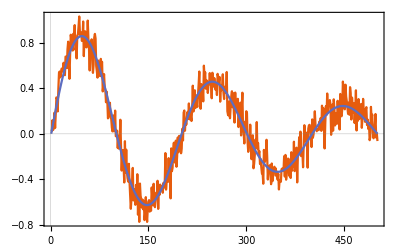

```mathematica
dx=5*Pi/500.0;
dataExact=Table[Sin[x]*Exp[-0.1*x],{x,0,5*Pi,dx}];
dataNoisy=Table[x+RandomVariate[NormalDistribution[0,0.1]],{x,dataExact}];
pltData=ListLinePlot[{dataNoisy,dataExact}]
```

```mathematica
diff[x_]:=(RotateLeft[x]-x)[[;;-2]]/(dx)
```

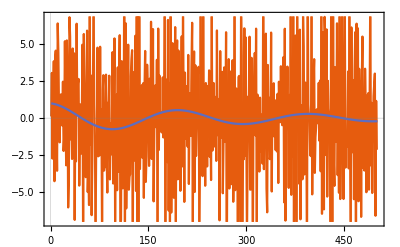

```mathematica
derivExact=Table[Cos[x]*Exp[-0.1*x]-0.1*Sin[x]*Exp[-0.1*x],{x,0,5*Pi,dx}];
derivNoisy=diff[dataNoisy];
pltDeriv=ListLinePlot[{derivNoisy,derivExact}]
```

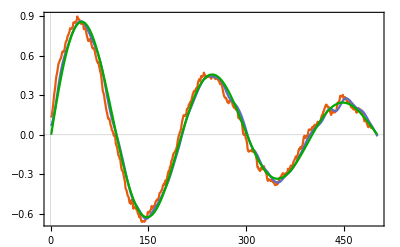

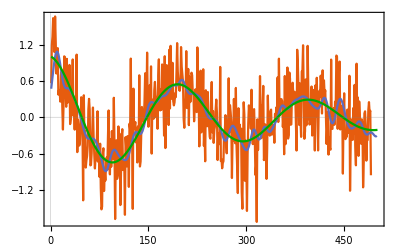

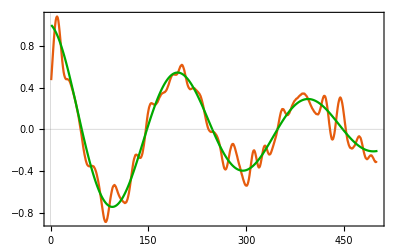

```mathematica
dataFiltered=LowpassFilter[dataNoisy,0.2];
dataAve=MovingAverage[dataNoisy,10];
ListLinePlot[{dataAve,dataFiltered,dataExact},PlotStyle->{Automatic,Automatic,Darker[Green]}]

derivFiltered=diff[dataFiltered];
derivAve=diff[dataAve];
ListLinePlot[{derivAve,derivFiltered,derivExact},PlotStyle->{Automatic,Automatic,Darker[Green]}]
ListLinePlot[{derivFiltered,derivExact},PlotStyle->{Automatic,Darker[Green]},PlotRange->All]
```

## Diff TVR

```mathematica
derivGuess=Flatten[{derivNoisy[[1]],derivNoisy,derivNoisy[[-1]]}];
noOptSteps=500;
alpha=0.1;
derivFinal=getDiffTVR[dataNoisy,derivGuess,noOptSteps,dx,alpha];
```

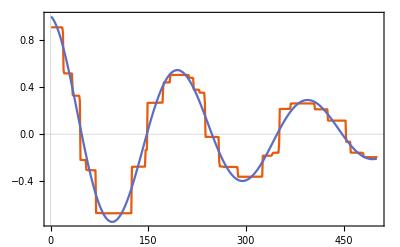
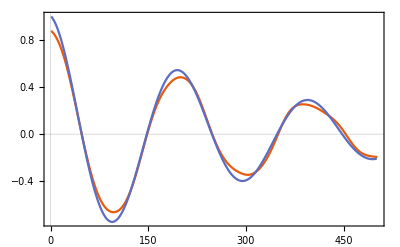

```mathematica
derivFinalFiltered=LowpassFilter[derivFinal,0.08];
Row[{
ListLinePlot[{derivFinal,derivExact},PlotRange->All],
ListLinePlot[{derivFinalFiltered,derivExact}]
}]
```

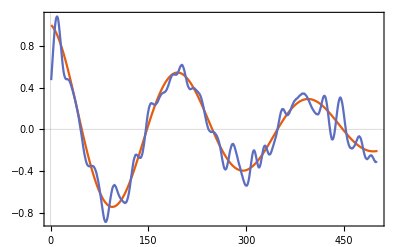
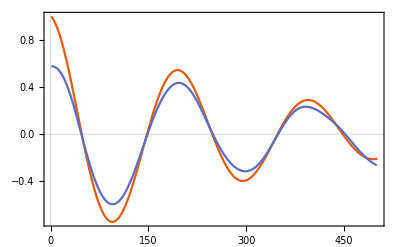

```mathematica
derivFilteredFiltered=LowpassFilter[derivFiltered,0.05];
Row[{
ListLinePlot[{derivExact,derivFiltered},PlotRange->All],
ListLinePlot[{derivExact,derivFilteredFiltered},PlotRange->All]
}]
```

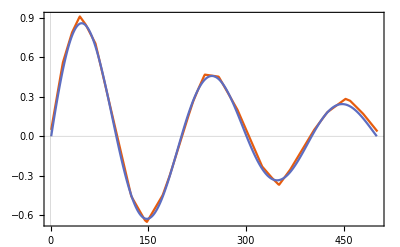
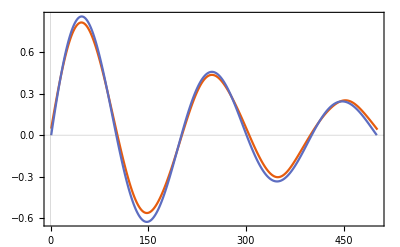
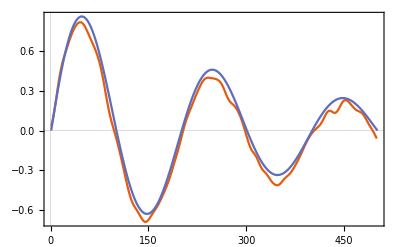
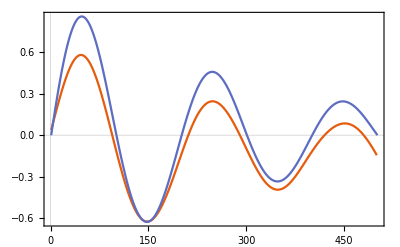

```mathematica
Row[{
ListLinePlot[{dataNoisy[[1]]+Accumulate[derivFinal]*dx,dataExact}],
ListLinePlot[{dataNoisy[[1]]+Accumulate[derivFinalFiltered]*dx,dataExact}],
ListLinePlot[{dataNoisy[[1]]+Accumulate[derivFiltered]*dx,dataExact}],
ListLinePlot[{dataNoisy[[1]]+Accumulate[derivFilteredFiltered]*dx,dataExact}]
}]
```